```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../Models/SMS-stop_SMQCD/SMS-stop_SMQCD",InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
```

```mathematica
FR$ClassesTranslation
```

{G→V(1),ghG→U(1),u→F(1),c→F(2),t→F(3),d→F(4),s→F(5),b→F(6),chi→F(7),ST→S(1)}

```mathematica
processGGtt =  { F[1],-F[1]} -> {-F[3], F[3]};
tops = CreateTopologies[1, 2->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
tops0 = CreateTopologies[0, 2->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
```

```mathematica
allDiags = InsertFields[tops,processGGtt, InsertionLevel-> {Particles},LastSelections->{S[1]}];
allDiags0 = InsertFields[tops0,processGGtt, InsertionLevel-> {Particles}];
```

in total: 1 Particles insertion

in total: 1 Particles insertion

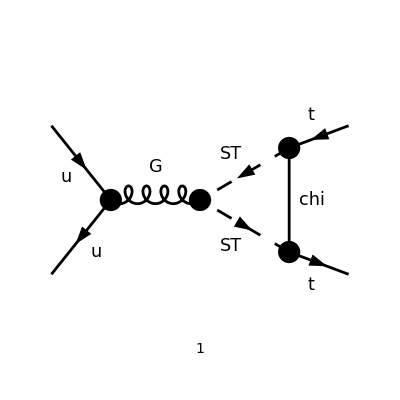

```mathematica
Paint[allDiags,ColumnsXRows->{1,1},ImageSize->{ 200,200},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

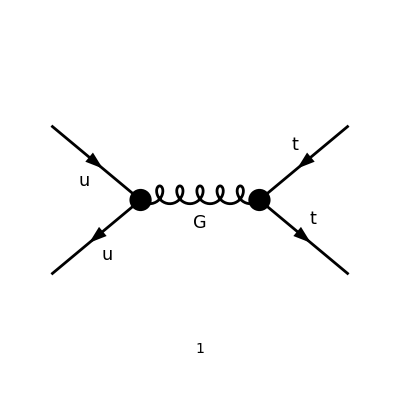

FeynArtsGraphics({u,u}→{t,t})(([1]))

```mathematica
Paint[allDiags0,ColumnsXRows->{1,1},ImageSize->{ 200,200},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True]
```

```mathematica
diags=DiagramExtract[allDiags,{1}];
diags0=DiagramExtract[allDiags0,{1}];
Paint[diags,ColumnsXRows->{2,1},ImageSize->{400,200},Numbering->Simple];
Paint[diags0,ColumnsXRows->{2,1},ImageSize->{400,200},Numbering->Simple];
```

-Graphics-

-Graphics-

```mathematica
(* Set Truncated->True to remove external fields  *)
amp[0]=FCFAConvert[CreateFeynAmp[diags,PreFactor->1,Truncated->True]/.{SUNT->FASUNT, GS-> √(4 Pi aS)},IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},LoopMomenta->{q},List->False,DropSumOver->True,SMP->True,List->False,LorentzIndexNames-> {μ,ν},Contract->False,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> M$FACouplings]
amp0[0]=FCFAConvert[CreateFeynAmp[diags0,PreFactor->1,Truncated->True]/.{SUNT->FASUNT, GS-> √(4 Pi aS)},IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},LoopMomenta->{q},List->False,DropSumOver->True,SMP->True,List->False,LorentzIndexNames-> {μ,ν},Contract->False,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> M$FACouplings]
```

in total: 1 Particles amplitude

-(2 √π √aS GS γ^μ g^μν T_Col2Col1^Glu5 T_Col4Col3^Glu5 (k1-k2+2 q)^ν (-ⅈ yDM (γ̄)^7).(mChi+γ·q).(-ⅈ yDM (γ̄)^6))/((k1+k2)^2 (q^2-mChi^2).((k1+q)^2-mST^2).((q-k2)^2-mST^2))

in total: 1 Particles amplitude

(ⅈ GS^2 γ^μ γ^ν g^μν T_Col2Col1^Glu5 T_Col4Col3^Glu5)/(k1+k2)^2

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,k1,k2,0,0,MT,MT];
```

```mathematica
amp[1]=(Contract[ SUNSimplify[FCTraceFactor[ amp[0]]]]/.{u-> 2 MT^2 -s-t})//Simplify
amp0[1]=(Contract[ SUNSimplify[FCTraceFactor[ amp0[0]]]]/.{u-> 2 MT^2 -s-t})//Simplify
```

(2 √π √aS GS yDM^2 T_Col2Col1^Glu5 T_Col4Col3^Glu5 (γ̄)^7.(mChi+γ·q).(γ̄)^6 γ·(k1-k2+2 q))/((k1+k2)^2 (q^2-mChi^2).((k1+q)^2-mST^2).((q-k2)^2-mST^2))

(ⅈ GS.GS (γ^ν)^2 T_Col2Col1^Glu5 T_Col4Col3^Glu5)/(k1+k2)^2

```mathematica
amp[2]=FullSimplify[DiracSimplify[amp[1]]]
```

(2 √π √aS GS yDM^2 (γ·q).(γ̄)^6 T_Col2Col1^Glu5 T_Col4Col3^Glu5 (γ·k1-γ·k2+2 γ·q))/((k1+k2)^2 (q^2-mChi^2).((k1+q)^2-mST^2).((k2-q)^2-mST^2))

```mathematica
amp[3]=TID[amp[2],q,UsePaVeBasis->True,PaVeAutoReduce->False,ToPaVe->True]//Simplify
```

1/(k1+k2)^2 4 ⅈ π^(5/2) √aS GS yDM^2 T_Col2Col1^Glu5 T_Col4Col3^Glu5 (γ^($AL($98)) γ^($AL($98)).(γ̄)^6 C_00(MT^2,s,MT^2,mChi^2,mST^2,mST^2)+1/2 (γ·k1-γ·k2) (γ·(k1-k2)).(γ̄)^6 C_1(MT^2,s,MT^2,mChi^2,mST^2,mST^2)+(γ·k1 (γ·k1).(γ̄)^6+γ·k2 (γ·k2).(γ̄)^6) C_11(MT^2,s,MT^2,mChi^2,mST^2,mST^2)-(γ·k2 (γ·k1).(γ̄)^6+γ·k1 (γ·k2).(γ̄)^6) C_12(MT^2,s,MT^2,mChi^2,mST^2,mST^2))

```mathematica
(* Make sure there are no divergences *)
UVpart = DiracSimplify[PaXEvaluateUV[amp[3]]]
```

(ⅈ π^(5/2) √aS GS yDM^2 γ^($AL($98)) T_Col2Col1^Glu5 T_Col4Col3^Glu5 γ^($AL($98)).(γ̄)^6)/(ε_UV (k1+k2)^2)

```mathematica
amp[5]=(DiracSimplify[amp[3]/.{u-> 2 MT^2 -s-t}])//FullSimplify
```

-1/s 4 ⅈ aS π^3 yDM^2 (2 s D_0(MT^2,0,0,MT^2+2 s,s+t,s,mChi^2,mST^2,mST^2,mST^2) (γ·k1).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3 mST^2+2 s (γ·k1).(γ̄)^6 D_1(MT^2,s+t,0,s,0,MT^2+2 s,mST^2,mChi^2,mST^2,mST^2) (T^Glu1 T^Glu2)_Col4Col3 mST^2+2 s (γ·p2).(γ̄)^6 D_2(MT^2,s+t,0,s,0,MT^2+2 s,mST^2,mChi^2,mST^2,mST^2) (T^Glu1 T^Glu2)_Col4Col3 mST^2+2 s (γ·p1).(γ̄)^6 D_3(MT^2,s+t,0,s,0,MT^2+2 s,mST^2,mChi^2,mST^2,mST^2) (T^Glu1 T^Glu2)_Col4Col3 mST^2+2 s (γ·p2).(γ̄)^6 D_3(MT^2,s+t,0,s,0,MT^2+2 s,mST^2,mChi^2,mST^2,mST^2) (T^Glu1 T^Glu2)_Col4Col3 mST^2+B_0(s+t,mChi^2,mST^2) ((γ·k1).(γ̄)^6-(γ·p2).(γ̄)^6) (T^Glu1 T^Glu2)_Col4Col3+(γ·k1).(γ̄)^6 B_1(MT^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col4Col3+(γ·k1).(γ̄)^6 B_1(s+t,mST^2,mChi^2) (T^Glu1 T^Glu2)_Col4Col3-(γ·p2).(γ̄)^6 B_1(s+t,mST^2,mChi^2) (T^Glu1 T^Glu2)_Col4Col3+MT^2 (γ·k1).(γ̄)^6 C_1(MT^2,MT^2+2 s,s,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col4Col3+s (γ·k1).(γ̄)^6 C_1(MT^2,MT^2+2 s,s,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col4Col3-t (γ·k1).(γ̄)^6 C_1(MT^2,MT^2+2 s,s,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col4Col3+s (γ·k1).(γ̄)^6 C_2(MT^2,MT^2+2 s,s,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col4Col3+2 s (γ·p1).(γ̄)^6 C_2(MT^2,MT^2+2 s,s,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col4Col3+2 s (γ·p2).(γ̄)^6 C_2(MT^2,MT^2+2 s,s,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col4Col3+2 (γ·p2).(γ̄)^6 C_00(MT^2,MT^2+2 s,s,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col4Col3+MT^2 (γ·k1).(γ̄)^6 C_11(MT^2,MT^2+2 s,s,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col4Col3-s (γ·k1).(γ̄)^6 C_11(MT^2,MT^2+2 s,s,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col4Col3-t (γ·k1).(γ̄)^6 C_11(MT^2,MT^2+2 s,s,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col4Col3+s (γ·k1).(γ̄)^6 C_12(MT^2,MT^2+2 s,s,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col4Col3+MT^2 (γ·p1).(γ̄)^6 C_12(MT^2,MT^2+2 s,s,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col4Col3-s (γ·p1).(γ̄)^6 C_12(MT^2,MT^2+2 s,s,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col4Col3-t (γ·p1).(γ̄)^6 C_12(MT^2,MT^2+2 s,s,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col4Col3+MT^2 (γ·p2).(γ̄)^6 C_12(MT^2,MT^2+2 s,s,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col4Col3-s (γ·p2).(γ̄)^6 C_12(MT^2,MT^2+2 s,s,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col4Col3-t (γ·p2).(γ̄)^6 C_12(MT^2,MT^2+2 s,s,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col4Col3+s (γ·p1).(γ̄)^6 C_22(MT^2,MT^2+2 s,s,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col4Col3+s (γ·p2).(γ̄)^6 C_22(MT^2,MT^2+2 s,s,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col4Col3-B_0(2 MT^2-t,mChi^2,mST^2) (γ·k2).(γ̄)^6 (T^Glu2 T^Glu1)_Col4Col3-(2 s D_0(MT^2,0,0,MT^2+2 s,2 MT^2-t,s,mChi^2,mST^2,mST^2,mST^2) (γ·k2).(γ̄)^6 mST^2+2 s (γ·p2).(γ̄)^6 D_2(MT^2,2 MT^2-t,0,s,0,MT^2+2 s,mST^2,mChi^2,mST^2,mST^2) mST^2+2 s (γ·p1).(γ̄)^6 D_3(MT^2,2 MT^2-t,0,s,0,MT^2+2 s,mST^2,mChi^2,mST^2,mST^2) mST^2+2 s (γ·p2).(γ̄)^6 D_3(MT^2,2 MT^2-t,0,s,0,MT^2+2 s,mST^2,mChi^2,mST^2,mST^2) mST^2-B_0(2 MT^2-t,mChi^2,mST^2) (γ·p2).(γ̄)^6-(γ·p2).(γ̄)^6 B_1(2 MT^2-t,mST^2,mChi^2)+2 s (γ·p1).(γ̄)^6 C_2(MT^2,MT^2+2 s,s,mST^2,mChi^2,mST^2)+2 s (γ·p2).(γ̄)^6 C_2(MT^2,MT^2+2 s,s,mST^2,mChi^2,mST^2)+2 (γ·p2).(γ̄)^6 C_00(MT^2,MT^2+2 s,s,mST^2,mChi^2,mST^2)-MT^2 (γ·p1).(γ̄)^6 C_12(MT^2,MT^2+2 s,s,mST^2,mChi^2,mST^2)+t (γ·p1).(γ̄)^6 C_12(MT^2,MT^2+2 s,s,mST^2,mChi^2,mST^2)-MT^2 (γ·p2).(γ̄)^6 C_12(MT^2,MT^2+2 s,s,mST^2,mChi^2,mST^2)+t (γ·p2).(γ̄)^6 C_12(MT^2,MT^2+2 s,s,mST^2,mChi^2,mST^2)+(γ·k2).(γ̄)^6 (B_1(MT^2,mChi^2,mST^2)+B_1(2 MT^2-t,mST^2,mChi^2)+(-MT^2+2 s+t) C_1(MT^2,MT^2+2 s,s,mST^2,mChi^2,mST^2)+(t-MT^2) C_11(MT^2,MT^2+2 s,s,mST^2,mChi^2,mST^2)+s (2 D_1(MT^2,2 MT^2-t,0,s,0,MT^2+2 s,mST^2,mChi^2,mST^2,mST^2) mST^2+C_2(MT^2,MT^2+2 s,s,mST^2,mChi^2,mST^2)+C_12(MT^2,MT^2+2 s,s,mST^2,mChi^2,mST^2)))+s ((γ·p1).(γ̄)^6+(γ·p2).(γ̄)^6) C_22(MT^2,MT^2+2 s,s,mST^2,mChi^2,mST^2)) (T^Glu2 T^Glu1)_Col4Col3+2 s C_0(MT^2,s,MT^2+2 s,mChi^2,mST^2,mST^2) ((γ·k1).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3-(γ·k2).(γ̄)^6 (T^Glu2 T^Glu1)_Col4Col3))

#### EFT Limit (s,t,u,MT →0)

```mathematica
FullSimplify[Expand[PaXEvaluate[amp[5],PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon),PaXSeries-> {{s,0,0},{MT,0,0},{t,0,0},{u,0,0}}]],Assumptions->{mST>0,mChi>0,μ>0}]
```

1/(144 π (mChi^2-mST^2)^4)ⅈ aS yDM^2 ((T^Glu1 T^Glu2)_Col4Col3 (3 (48 mChi^4 mST^2-15 mChi^2 mST^4+12 (2 mChi^4 mST^2+3 mChi^6) log(mChi/mST)-37 mChi^6+4 mST^6) (γ·k1).(γ̄)^6+(-81 mChi^4 mST^2+54 mChi^2 mST^4+12 mChi^4 (3 mST^2-4 mChi^2) log(mChi/mST)+38 mChi^6-11 mST^6) (γ·p1).(γ̄)^6+(-81 mChi^4 mST^2+27 mChi^2 mST^4+12 mChi^4 (5 mChi^2+3 mST^2) log(mST/mChi)+61 mChi^6-7 mST^6) (γ·p2).(γ̄)^6)+(T^Glu2 T^Glu1)_Col4Col3 (3 (-48 mChi^4 mST^2+15 mChi^2 mST^4+12 mChi^4 (3 mChi^2+2 mST^2) log(mST/mChi)+37 mChi^6-4 mST^6) (γ·k2).(γ̄)^6+(18 mChi^4 mST^2-9 mChi^2 mST^4+12 mChi^6 log(mChi/mST)-11 mChi^6+2 mST^6) (4 (γ·p1).(γ̄)^6+5 (γ·p2).(γ̄)^6)))

```mathematica
Limit[%,mChi-> mST]
```

1/(96 π mST^2)ⅈ aS yDM^2 (7 (γ·k1).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3-7 (γ·k2).(γ̄)^6 (T^Glu2 T^Glu1)_Col4Col3+(γ·p1).(γ̄)^6 (4 (T^Glu2 T^Glu1)_Col4Col3-5 (T^Glu1 T^Glu2)_Col4Col3)-4 (γ·p2).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3+5 (γ·p2).(γ̄)^6 (T^Glu2 T^Glu1)_Col4Col3)

```mathematica
Collect[Expand[%28],DiracGamma[x_,D]]
```

(7 ⅈ aS yDM^2 (γ·k1).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3)/(96 π mST^2)-(7 ⅈ aS yDM^2 (γ·k2).(γ̄)^6 (T^Glu2 T^Glu1)_Col4Col3)/(96 π mST^2)-(5 ⅈ aS yDM^2 (γ·p1).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3)/(96 π mST^2)+(ⅈ aS yDM^2 (γ·p1).(γ̄)^6 (T^Glu2 T^Glu1)_Col4Col3)/(24 π mST^2)-(ⅈ aS yDM^2 (γ·p2).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3)/(24 π mST^2)+(5 ⅈ aS yDM^2 (γ·p2).(γ̄)^6 (T^Glu2 T^Glu1)_Col4Col3)/(96 π mST^2)

```mathematica
Collect[Expand[%43]/.{DiracGamma[Momentum[x_,D],D].DiracGamma[6]-> GS[x] Subscript[P, L]},{GS[p1],GS[p2],GS[k1],GS[k2]},Simplify]
```

(7 ⅈ aS yDM^2 P_L γ̄·OverBar[k1] (T^Glu1 T^Glu2)_Col4Col3)/(96 π mST^2)-(7 ⅈ aS yDM^2 P_L γ̄·OverBar[k2] (T^Glu2 T^Glu1)_Col4Col3)/(96 π mST^2)-(ⅈ aS yDM^2 P_L γ̄·OverBar[p1] (5 (T^Glu1 T^Glu2)_Col4Col3-4 (T^Glu2 T^Glu1)_Col4Col3))/(96 π mST^2)-(ⅈ aS yDM^2 P_L γ̄·OverBar[p2] (4 (T^Glu1 T^Glu2)_Col4Col3-5 (T^Glu2 T^Glu1)_Col4Col3))/(96 π mST^2)